# Initialization strategies for Deep Neural Networks

In this computational essay, we explore how different initialization strategies for neural networks can lead to unstable activations as we do forward propagation.

Yash Akhauri, Jun. 24,  2018

We conduct an exploration of how activations diminish as the network depth increases, provided the initialization strategy of the network is inappropriate. We have to make several important and subtle choices when we attempt to train Deep Neural networks, and the rate of convergence of such a neural network can greatly depend on the initial conditions of the network as well.

## Forward propagation in neural networks

A typical deep neural network can be imagine as a series of matrix multiplications. Neural networks are trained by minimizing a loss function by changing the weights of the neural network. The gradient of a network always points in the direction of steepest increase, and we have to calculate the gradient of the loss with respect to the weights and move in the opposite direction.

As propagation in a vanilla neural network is a series of matrix multiplications, it becomes obvious that if the outputs of the network tend to zero, the gradients do too. If we initialize several matrices as done below,  and draw from different distributions, we can see vanishing or exploding results of the matrix multiplication.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code 
(* Experiment with the Normal Distribution properties to see how the product result histogram explodes/vanishes. *)
```

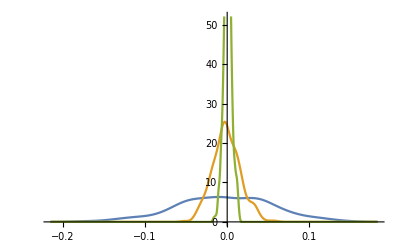

```mathematica
SeedRandom[91];
a = RandomVariate[NormalDistribution[0, 0.06], {20, 20}];
b = RandomVariate[NormalDistribution[0, 0.06], {20, 20}];c = RandomVariate[NormalDistribution[0, 0.06], {20, 20}];
h={Flatten[a], Flatten[a.b], Flatten[a.b.c]};
SmoothHistogram[h[[#]]&/@Range[3]]
```

## Extending to neural networks

Here, we extend the idea demonstrated above to real neural networks built using the WolfrmaLanguage.

Let us initialize a NetGraph so that we can study the intermediate activations of a neural network for a specific input.

```mathematica
SeedRandom[21];
dim=30;
net=NetChain[{LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim],LinearLayer[dim]}, "Input"-> 100];
inputvec=RandomVariate[NormalDistribution[], 100];
```

Let us initialize the network with the Identity strategy, drawing from a normal distribution with  μ = 0 and σ = 0.09.

```mathematica
netinit = NetInitialize[net, Method ->{"Identity", "Distribution"->NormalDistribution[0, 0.09]}];
outputs = netinit[inputvec, {NetPort[1, "Output"],NetPort[4, "Output"],NetPort[8, "Output"],NetPort[10, "Output"],NetPort[12, "Output"],NetPort[13, "Output"],NetPort[14, "Output"]}];
h = outputs[[#]]&/@Range[7]; 
SmoothHistogram3D[Transpose[{ConstantArray[#,Length[h[[#]]]],h[[#]]}]&/@Range[7]]
```

-Graphics3D-

Let us initialize the network with the Identity strategy, drawing from a normal distribution with  μ = 0 and σ = 0.13.

```mathematica
netinit = NetInitialize[net, Method ->{"Identity", "Distribution"->NormalDistribution[0, 0.13]}];
outputs = netinit[inputvec, {NetPort[1, "Output"],NetPort[4, "Output"],NetPort[8, "Output"],NetPort[10, "Output"],NetPort[12, "Output"],NetPort[13, "Output"],NetPort[14, "Output"]}];
h = outputs[[#]]&/@Range[7]; 
SmoothHistogram3D[Transpose[{ConstantArray[#,Length[h[[#]]]],h[[#]]}]&/@Range[7]]
```

-Graphics3D-

Finally, let us attempt the well known Xavier Initialization strategy.

```mathematica
netinit = NetInitialize[net, Method ->{"Xavier"}];
outputs = netinit[inputvec, {NetPort[1, "Output"],NetPort[4, "Output"],NetPort[8, "Output"],NetPort[10, "Output"],NetPort[12, "Output"],NetPort[13, "Output"],NetPort[14, "Output"]}];
h = outputs[[#]]&/@Range[7]; 
SmoothHistogram3D[Transpose[{ConstantArray[#,Length[h[[#]]]],h[[#]]}]&/@Range[7]]
```

-Graphics3D-

It becomes quite evident that the Xavier initialization strategy will lead to much stronger propagation of gradients and faster convergence.

## Further explorations

It will be a good exercise to experiment with different initialization strategies and inspecting its effects on different architectures of neural networks.

## Author contact information

akhauri.yash@gmail.com